```mathematica
(*Generates all figures for Fig. 2 of Supplemental Material - power laws of the imaginary part of the disorder-averaged charge susceptibility.*)
(*Takes a ~1.5 hours to run on my laptop.*)
(*Set notebook directory.*)
SetDirectory[NotebookDirectory[]];

(*Assorted graphics commands.*)
linelegs[label_,legs_,pos_,cols_]:=PlotLegends->Placed[LineLegend[Table[Text[Style[legs[[i]],14,FontFamily->"Times New Roman"]],{i,1,Length[legs]}],LegendLabel->Text[Style[label,14,FontFamily->"Times New Roman"]],LabelStyle->{GrayLevel[0],14},LegendLayout->{"Column",cols}],pos]
frameStyle[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->True,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}
text[x0_,y0_,txt_,color_]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",14],{x0,y0}]]
text[x0_,y0_,txt_,color_,size_:fontSize]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",size],{x0,y0}]]
Cell[StyleData["Print"],FontSize->36];

(*Non-universal constants, set to 1 for the purposes of these plots.*)
a=1;
b=1;
ρ=1;
m=1;
```

```mathematica
(*Expressed in terms of real frequency and wave vector, e set to 10^-4 for all plots.*)
AvgImχnn[ω_,q_,Δ_,δp_]:=NIntegrate[(((ρ^2 a/m^2)q^4 √(b*ω^2*Abs[Log[Abs[dps]]]-dps^2))/((ρ ω^2-a q^2 dps-(4π ρ^2(10^-4)^2)/m^2)^2+a^2*b*q^4*ω^2*Abs[Log[Abs[dps]]]-a^2 q^4 dps^2))(1/(√(2π)Δ)Exp[-(dps-δp)^2/(2*Δ^2)]),{dps,-Exp[-1/2 ProductLog[0,2/(b*ω^2)]],Exp[-1/2 ProductLog[0,2/(b*ω^2)]]},WorkingPrecision->18];
Imχnn[ω_,q_,δp_]:=Piecewise[{{((ρ^2 a/m^2)q^4 √(b*ω^2*Abs[Log[Abs[δp]]]-δp^2))/((ρ ω^2-a q^2 δp-(4π ρ^2(10^-4)^2)/m^2)^2+a^2*b*q^4*ω^2*Abs[Log[Abs[δp]]]-a^2 q^4 δp^2),ω>1/(√b)Abs[δp]/(√Abs[Log[Abs[δp]]])},{0,ω≤ 1/(√b)Abs[δp]/(√Abs[Log[Abs[δp]]])}}];
```

```mathematica
(*Logarithmic derivatives to find regions of (ω,q) where -χ''~q^αω^β.*)
dlogImχnndlogω1[logω_,q_,δp_]=D[Log[Imχnn[Exp[logω],q,δp]],logω];
dlogImχnndlogq1[ω_,logq_,δp_]=D[Log[Imχnn[ω,Exp[logq],δp]],logq];
loglogImχnndω[ω_,q_,δp_]=dlogImχnndlogω1[Log[ω],q,δp];
loglogImχnndq[ω_,q_,δp_]=dlogImχnndlogq1[ω,Log[q],δp];
```

```mathematica
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

Paclet[MaTeX,1.7.9,<>]

```mathematica
MaTeX["-\chi'' \sim q^{4} \omega^{-3}"]
```

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

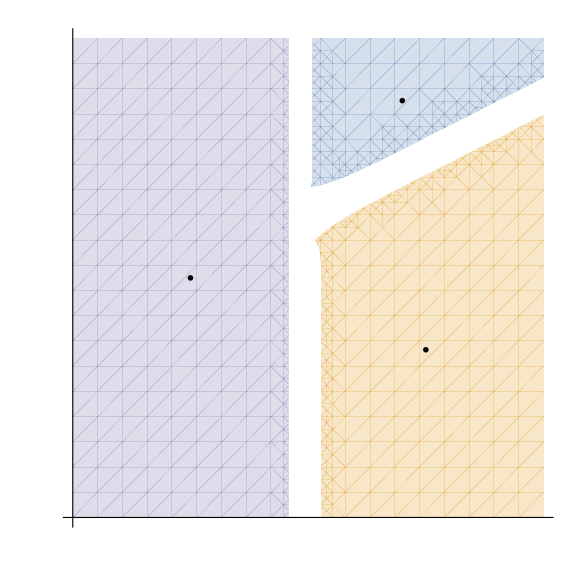

```mathematica
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogImχnndω[Exp[logω],Exp[logq],-10^-3]-(-1)]<0.1&&Abs[loglogImχnndq[Exp[logω],Exp[logq],-10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]}];
rplotb=RegionPlot[{Abs[loglogImχnndω[Exp[logω],Exp[logq],-10^-3]-(-3)]<0.1&&Abs[loglogImχnndq[Exp[logω],Exp[logq],-10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]}];
rplotc=RegionPlot[{Abs[Imχnn[Exp[logω],Exp[logq],-10^-3]]==0},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[5]]}];
exp1=text[-0.5Log[10],-4.5Log[10],MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-1Log[10],0.7Log[10],MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-5.5Log[10],-3Log[10],MaTeX["\equiv 0",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
Show[rplota,rplotb,rplotc,exp1,exp2,exp3,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=-10^{-3}; \; \sigma=0",Magnification->3.5]]
```

```mathematica
Quiet[
dlogAvgImχnndlogω1[logω_,q_,Δ_,δp_]=D[Log[AvgImχnn[Exp[logω],q,Δ,δp]],logω];
dlogAvgImχnndlogq1[ω_,logq_,Δ_,δp_]=D[Log[AvgImχnn[ω,Exp[logq],Δ,δp]],logq];
loglogAvgImχnndω[ω_,q_,Δ_,δp_]=dlogAvgImχnndlogω1[Log[ω],q,Δ,δp];
loglogAvgImχnndq[ω_,q_,Δ_,δp_]=dlogAvgImχnndlogq1[ω,Log[q],Δ,δp];
]
```

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-29 ⅇ^(-50000000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (5000 ⅇ^(-50000000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((1.05187 ⅇ^(-50000000 (1/1000+dps)^2) √(-dps^2+1.×10^-6 Abs[Log[Abs[dps]]]))/((8.74336×10^-7-0.0162378 dps)^2-0.000263665 dps^2+2.63665×10^-10 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-3565.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2077.38] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26562.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.0013265495904849662320962972059476045300565846449633648344416422638678}. NIntegrate obtained 0.24711466790409015219724892251182448611047201797332208019162881255242 and 0.0016896754808109644473961278452489534626807871370767954281274515887053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.0013265495904849662320962972059476045300565846449633648344416422638678}. NIntegrate obtained -0.27941424907161526344761662815705954803878658337682490627723684954771 and 0.0019182865195372151294935042952438060876030951187339976366628269331055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.0012302970326408175707920588200573112586879528294737767927856489798896}. NIntegrate obtained 0.021893688202378951842709555695069463436233488314894956771040077839284 and 2.9519287160562030841723094213768383490786465775358360971595231575348×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-29 ⅇ^(-50000000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (5000 ⅇ^(-50000000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((4.50343×10^-28 ⅇ^(-50000000 (1/1000+dps)^2) √(-dps^2+0.0000112884 Abs[Log[Abs[dps]]]))/((0.0000111627-3.35983×10^-16 dps)^2-1.12884×10^-31 dps^2+1.27428×10^-36 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-3565.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2077.38] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3565.01] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.0013290014727856672453254620601598712160037771807967364303087515860775}. NIntegrate obtained 0.00023269964724403806528081731788816896455135737544106025748425580243073 and 7.4614486014705293737294667352076085221396097988810108980631585611997×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.0013290014727856672453254620601598712160037771807967364303087515860775}. NIntegrate obtained -0.00069768204944602303399759902416679522224969943634120512989622363104632 and 2.2370891648402691864048282046560750633479137510969344625170070196453×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.0013290014727856672453254620601598712160037771807967364303087515860775}. NIntegrate obtained 0.00092997201704040397114907406806499021112112339470959628296803864981542 and 2.9819104114337169261362209044194256977381339642999678361576068779353×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-29 ⅇ^(-50000000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (5000 ⅇ^(-50000000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((0.00825465 ⅇ^(-50000000 (1/1000+dps)^2) √(-dps^2+8.85867×10^-8 Abs[Log[Abs[dps]]]))/((-3.7077×10^-8-0.00143845 dps)^2-2.06913×10^-6 dps^2+1.83298×10^-13 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00079513705766138164914288034690717167827726346690288308900592264454567}. NIntegrate obtained 129.39044972200210069222546914191562363488551164002521362902879581691-0.000018119857008731230818517881846327522422363464924809804385609014522418 ⅈ and 0.000016900198354994598650566205202299558442876462438130135662598661119855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00079513705766138164914288034690717167827726346690288308900592264454567}. NIntegrate obtained 124.71129964919601109101937554457287371027360092913517280298257729873-0.000017061980210691609440425306023404031013604767324512740086655074436549 ⅈ and 0.000015906663718856663835399117592752791486024735280740449669325401324276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00079513705766138164914288034690717167827726346690288308900592264454567}. NIntegrate obtained 124.30552434764067809695025845708607201360965893592497410862637076076-0.00001697276206262019386031755301421439138192109686026764610657444367718 ⅈ and 0.000015822895202628472155928856990098126033115831834851269785919975007037 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-29 ⅇ^(-50000000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (5000 ⅇ^(-50000000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (5000 ⅇ^(-50000000 (1/1000+dps)^2) √(2/π) ((4.00002×10^-32 √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])-(1.×10^-32 (-4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps) dps-4.00002×10^-32 dps^2+4.00003×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-8.0016374576724895319274160918981999016931041218693590103227969040211×10^-6}. NIntegrate obtained 2.0711765933968021385215166261250628390479446876068884145669612651059×10^-19 and 6.1406012893282675273160189859770579333197826672215797791557060764176×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-2.496939045509039596957179400680804616505198340244318868568220926366×10^-6}. NIntegrate obtained 2.7431703637707348092766436040782414813698514125792212193305189202056×10^-19-3.4474290752191390537204645276791712584073880861016095726051888114983×10^-27 ⅈ and 4.8143348479651001303805949198941174414321022052359021199313266177993×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-4.4722576377154426426743491475020979731570461357942063000080778714067×10^-6}. NIntegrate obtained 1.0390958952508614370303006002940685456636071270978958873018929204248×10^-18-1.1825938124078918990443556984781479910815969686088357977583660981806×10^-25 ⅈ and 1.4928358928578300479282269381380089509765847102415971823732313872907×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

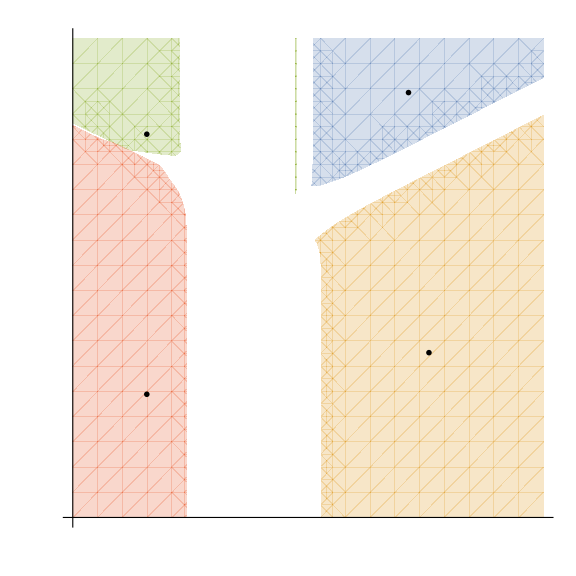

```mathematica
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-4,-10^-3]-(-1)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-4,-10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]},"NumericalFunction"->False];
rplotb=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-4,-10^-3]-(-3)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-4,-10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]},"NumericalFunction"->False];
rplotc=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-4,-10^-3]-(0)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-4,-10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[3]]},"NumericalFunction"->False];
rplotd=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-4,-10^-3]-(2)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-4,-10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[4]]},"NumericalFunction"->False];
exp1=text[-1.0,-10.5,MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-2,2,MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-14.8,0,MaTeX["\sim q^{0} \omega^{0}",Magnification->3.5],GrayLevel[0],fs];
exp4=text[-14.8,-12.5,MaTeX["\sim q^{4} \omega^{2}",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
Show[rplota,rplotb,rplotc,rplotd,exp1,exp2,exp3,exp4,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=-10^{-3}; \; \sigma=10^{-4}",Magnification->3.5]]
```

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((0.105187 ⅇ^(-500000 (1/1000+dps)^2) √(-dps^2+0.0000112884 Abs[Log[Abs[dps]]]))/((0.0000111627-0.0162378 dps)^2-0.000263665 dps^2+2.97634×10^-9 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-2054.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1928.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2054.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((4.50343×10^-29 ⅇ^(-500000 (1/1000+dps)^2) √(-dps^2+1.×10^-6 Abs[Log[Abs[dps]]]))/((8.74336×10^-7-3.35983×10^-16 dps)^2-1.12884×10^-31 dps^2+1.12884×10^-37 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-2054.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1928.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14572.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((0.000825465 ⅇ^(-500000 (1/1000+dps)^2) √(-dps^2+6.15849×10^-11 Abs[Log[Abs[dps]]]))/((-1.25602×10^-7-0.00143845 dps)^2-2.06913×10^-6 dps^2+1.27427×10^-16 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857092504812431879471163024351163426582104629861190599283}. NIntegrate obtained 642.6551392422032154237816952874232663219857672701601056459304596721-0.0042210587948978798482434897801953234607692908480294571120484744470625 ⅈ and 0.0064980925587323214360238051357440266660964083920190513783342844403132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.000025521015728491960361283207476159189323929453322527358204886183469312}. NIntegrate obtained -4.002181113460159889027856301326586095504503666648197307989685992643 and 9.2358051531431470977868041423584144323153252068239341373975043577418×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00025482984479425963486303027010513903841387683140406798600622657231396}. NIntegrate obtained -8.4256321459352477090400370286191086319136804054789642254554868038727-5.4813060281278602852139618169061773094240090612138476335163083278029×10^-6 ⅈ and 7.1333048496035879753744441247490420223093249924682678919209772325874×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (1/1000+dps)^2) √(2/π) ((4.00002×10^-32 √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])-(1.×10^-32 (-4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps) dps-4.00002×10^-32 dps^2+4.00003×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00025482984479425963486303027010513903841387683140406798600622657231396}. NIntegrate obtained -8.4256321459352477090400370286191086319136804054789642254554868038727-5.4813060281278602852139618169061773094240090612138476335163083278029×10^-6 ⅈ and 7.1333048496035879753744441247490420223093249924682678919209772325874×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857092504812431879471163024351163426582104629861190599283}. NIntegrate obtained 642.6551392422032154237816952874232663219857672701601056459304596721-0.0042210587948978798482434897801953234607692908480294571120484744470625 ⅈ and 0.0064980925587323214360238051357440266660964083920190513783342844403132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-2.496939045509039596957179400680804616505198340244318868568220926366×10^-6}. NIntegrate obtained 78.630318755370195444404430357217472971208837947991931330319586569201-8.7171084755342826674039913793045491203938686101426031948230613600044×10^-7 ⅈ and 1.3031111499918743138103325332177599377723620988319611134508118947614×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

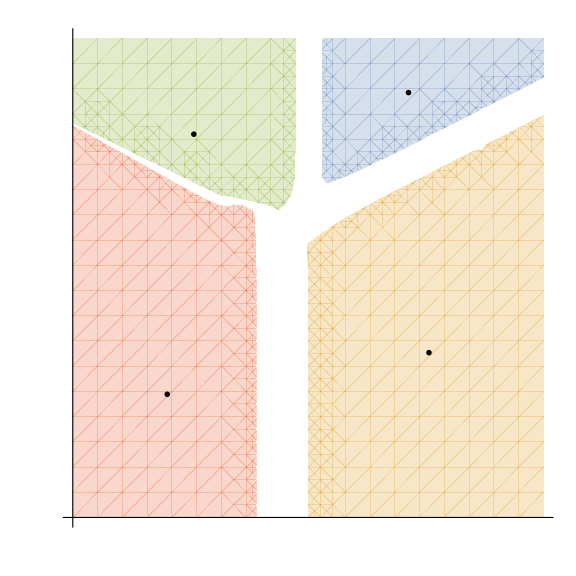

```mathematica
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,-10^-3]-(-1)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,-10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]},"NumericalFunction"->False];
rplotb=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,-10^-3]-(-3)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,-10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]},"NumericalFunction"->False];
rplotc=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,-10^-3]-(0)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,-10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[3]]},"NumericalFunction"->False];
rplotd=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,-10^-3]-(2)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,-10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[4]]},"NumericalFunction"->False];
exp1=text[-1.0,-10.5,MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-2,2,MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-12.5,0,MaTeX["\sim q^{0} \omega^{0}",Magnification->3.5],GrayLevel[0],fs];
exp4=text[-13.8,-12.5,MaTeX["\sim q^{4} \omega^{2}",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
Show[rplota,rplotb,rplotc,rplotd,exp1,exp2,exp3,exp4,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=-10^{-3}; \; \sigma=10^{-3}",Magnification->3.5]]
```

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-31 ⅇ^(-5000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (50 ⅇ^(-5000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((1.34037 ⅇ^(-5000 (1/1000+dps)^2) √(-dps^2+0.000127427 Abs[Log[Abs[dps]]]))/((0.000127302-0.183298 dps)^2-0.0335981 dps^2+4.28132×10^-6 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-830.399] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-822.273] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2878.42] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-31 ⅇ^(-5000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (50 ⅇ^(-5000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((4.50343×10^-30 ⅇ^(-5000 (1/1000+dps)^2) √(-dps^2+0.000127427 Abs[Log[Abs[dps]]]))/((0.000127302-3.35983×10^-16 dps)^2-1.12884×10^-31 dps^2+1.43846×10^-35 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-830.399] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-822.273] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2878.42] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-31 ⅇ^(-5000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (50 ⅇ^(-5000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((6.47793×10^-7 ⅇ^(-5000 (1/1000+dps)^2) √(-dps^2+7.8476×10^-9 Abs[Log[Abs[dps]]]))/((-1.17816×10^-7-0.000127427 dps)^2-1.62378×10^-8 dps^2+1.27427×10^-16 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00079513705766138164914288034690717167827726346690288308900592264454567}. NIntegrate obtained -5.8084173710755640737721069993152206739587765004713290885527187341453-3.564099709247258538833606818592189565586967040469214891286350371647×10^-6 ⅈ and 3.5791457854435306940278327234548155275748662593486165060762241516287×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00025482984479425963486303027010513903841387683140406798600622657231396}. NIntegrate obtained -0.98670462780209661340155347128577199047865881314532486231854322982975-1.0723745712760024622701409959202850657645877218318161736848323206539×10^-6 ⅈ and 1.2098244567856678369770367856127016562683668708019004332797328195237×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.0024517264958439519381846577399534460680378632719437049044290362850053}. NIntegrate obtained -1.1645737988076931022841561717060927130136489537712612722851170899799 and 1.8235998047387781189026812286686214492844665856721922931131684168804×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-31 ⅇ^(-5000 (1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (50 ⅇ^(-5000 (1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (50 ⅇ^(-5000 (1/1000+dps)^2) √(2/π) ((4.00002×10^-32 √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])-(1.×10^-32 (-4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps) dps-4.00002×10^-32 dps^2+4.00003×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857078649866975616039967490286052126863416717624271455948}. NIntegrate obtained 0.87416679166909478540371571382772885508010975756965165137143543963044-1.6178960229608396416263716924697203490247977834582691812332419356879×10^-8 ⅈ and 1.5456765200360188302824601619344988690761538931174998565396238232571×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857092504812431879471163024351163426582104629861190599283}. NIntegrate obtained 98.07863974495133116679117101763645461943883013349528733265223916157-0.00064122188201853999713982148283803017189333832980532876275678684493386 ⅈ and 0.0009872946059594766651809478492320251318900550699004465651634237171711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-2.496939045509039596957179400680804616505198340244318868568220926366×10^-6}. NIntegrate obtained 12.88913918296483580026043697028553811928741410745470222191280650675-1.4270290354391748046195744528495353768777631548197660763050298166205×10^-7 ⅈ and 2.1349827490423168944973109361088382018725360383122173690587177644018×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

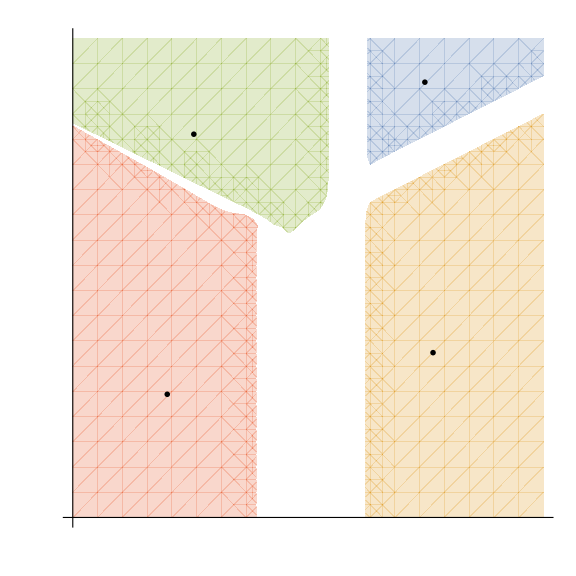

```mathematica
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-2,-10^-3]-(-1)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-2,-10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]},"NumericalFunction"->False];
rplotb=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-2,-10^-3]-(-3)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-2,-10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]},"NumericalFunction"->False];
rplotc=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-2,-10^-3]-(0)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-2,-10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[3]]},"NumericalFunction"->False];
rplotd=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-2,-10^-3]-(2)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-2,-10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[4]]},"NumericalFunction"->False];
exp1=text[-0.8,-10.5,MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-1.2,2.5,MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-12.5,0,MaTeX["\sim q^{0} \omega^{0}",Magnification->3.5],GrayLevel[0],fs];
exp4=text[-13.8,-12.5,MaTeX["\sim q^{4} \omega^{2}",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
Show[rplota,rplotb,rplotc,rplotd,exp1,exp2,exp3,exp4,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=-10^{-3}; \; \sigma=10^{-2}",Magnification->3.5]]
```

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 dps^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 dps^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((0.000825465 ⅇ^(-500000 dps^2) √(-dps^2+1.×10^-6 Abs[Log[Abs[dps]]]))/((8.74336×10^-7-0.00143845 dps)^2-2.06913×10^-6 dps^2+2.06913×10^-12 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-1990.55] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 dps^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 dps^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((4.50343×10^-29 ⅇ^(-500000 dps^2) √(-dps^2+0.0000112884 Abs[Log[Abs[dps]]]))/((0.0000111627-3.35983×10^-16 dps)^2-1.12884×10^-31 dps^2+1.27428×10^-36 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-1990.55] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14402.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 dps^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 dps^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((6.47793×10^-6 ⅇ^(-500000 dps^2) √(-dps^2+7.8476×10^-9 Abs[Log[Abs[dps]]]))/((-1.17816×10^-7-0.000127427 dps)^2-1.62378×10^-8 dps^2+1.27427×10^-16 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00079513705766138164914288034690717167827726346690288308900592264454567}. NIntegrate obtained -78.637476837228117587847815470996573502953860568053082545248605460122-0.000026001252059520418093162156893680200143405960179292987574684626801903 ⅈ and 0.000026141416121704348625502260636273970615585276800792974138604383602266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00025482984479425963486303027010513903841387683140406798600622657231396}. NIntegrate obtained -19.013518083188632709895203223567110340297435789623112396643416282209-7.0254757724611977929898786493077344331199628387265030844566664754622×10^-6 ⅈ and 0.000014239321799887327746140250501495781759046157138968365441642146265925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00079513705766138164914288034690717167827726346690288308900592264454567}. NIntegrate obtained -82.475440561004250307328252184241744576199250021681941799782917883274-0.000012384067286141229542001488304131973472232471699595312238300313982528 ⅈ and 0.000014945286850217289551218753812086334319753073859868866603670913768635 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 dps^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 dps^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 dps^2) √(2/π) ((4.00002×10^-32 √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])-(1.×10^-32 (-4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps) dps-4.00002×10^-32 dps^2+4.00003×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857078649866975616039967490286052126863416717624271455948}. NIntegrate obtained 8.7710405937816203110573134744185630823292256286185665772394590823448-1.6205268144219552124706302755547832403616793759807144271203554563473×10^-7 ⅈ and 1.5481917515567872018049006323146891816208827593530492354228233856814×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857092504812431879471163024351163426582104629861190599283}. NIntegrate obtained 981.21467633022087196526080059642556164329877697101245412576847063842-0.0064183031040603629939136753231317713858325275664753534359678333340919 ⅈ and 0.0098823836517906523131556224083602911780369328867726222623301898569301 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-2.496939045509039596957179400680804616505198340244318868568220926366×10^-6}. NIntegrate obtained 129.53620295720209730333796692801051256426395351963360585280614528281-1.434147054788311080955663287105087876176782023586068923684775301513×10^-6 ⅈ and 2.1456496671333528123696168252765530029679188575532522969736000435312×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

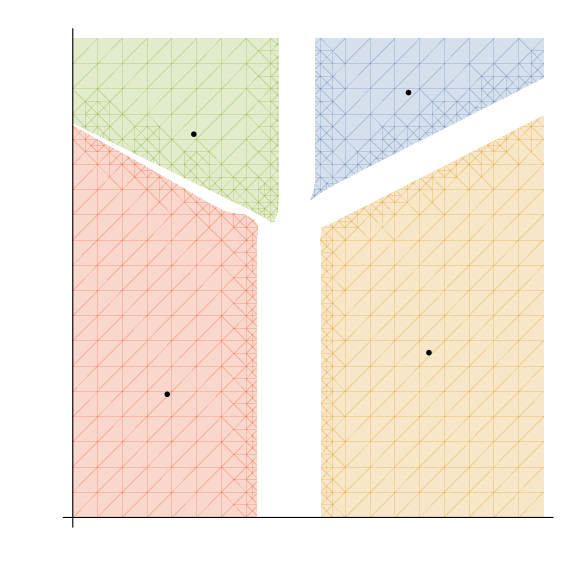

```mathematica
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,0]-(-1)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,0]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]},"NumericalFunction"->False];
rplotb=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,0]-(-3)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,0]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]},"NumericalFunction"->False];
rplotc=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,0]-(0)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,0]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[3]]},"NumericalFunction"->False];
rplotd=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,0]-(2)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,0]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[4]]},"NumericalFunction"->False];
exp1=text[-1.0,-10.5,MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-2,2,MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-12.5,0,MaTeX["\sim q^{0} \omega^{0}",Magnification->3.5],GrayLevel[0],fs];
exp4=text[-13.8,-12.5,MaTeX["\sim q^{4} \omega^{2}",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
Show[rplota,rplotb,rplotc,rplotd,exp1,exp2,exp3,exp4,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=0; \; \sigma=10^{-3}",Magnification->3.5]]
```

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/10000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/10000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((0.000825465 ⅇ^(-500000 (-1/10000+dps)^2) √(-dps^2+1.×10^-6 Abs[Log[Abs[dps]]]))/((8.74336×10^-7-0.00143845 dps)^2-2.06913×10^-6 dps^2+2.06913×10^-12 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-1984.25] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1996.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1984.25] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/10000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/10000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((4.50343×10^-29 ⅇ^(-500000 (-1/10000+dps)^2) √(-dps^2+0.0000112884 Abs[Log[Abs[dps]]]))/((0.0000111627-3.35983×10^-16 dps)^2-1.12884×10^-31 dps^2+1.27428×10^-36 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-1984.25] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1996.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14385.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/10000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/10000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((6.47793×10^-6 ⅇ^(-500000 (-1/10000+dps)^2) √(-dps^2+7.8476×10^-9 Abs[Log[Abs[dps]]]))/((-1.17816×10^-7-0.000127427 dps)^2-1.62378×10^-8 dps^2+1.27427×10^-16 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00079513705766138164914288034690717167827726346690288308900592264454567}. NIntegrate obtained -41.773650065186060763515671581935770204672587299088985225108354706381-0.000024040167206011644307300475720809341133937901883073831881813722760873 ⅈ and 0.000024465928615966812556638490533446055039089370423714901092510842508888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00025482984479425963486303027010513903841387683140406798600622657231396}. NIntegrate obtained -18.408934825144554318861310695966484819801288572783609592862477317842-6.8016217527266823736660157118804681082834827525794859729036865475254×10^-6 ⅈ and 0.000011963755238666069577491858156956783052455146463264024689703295797965 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.00079513705766138164914288034690717167827726346690288308900592264454567}. NIntegrate obtained -78.145184528711638001923247862466664375700312412872306897904763599067-0.000011880340410467030857256968330598044990291515368480709986574711446454 ⅈ and 0.000014635041421451827598404275425703049021516709930499660677916995806893 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/10000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/10000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/10000+dps)^2) √(2/π) ((4.00002×10^-32 √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])-(1.×10^-32 (-4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps) dps-4.00002×10^-32 dps^2+4.00003×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857078649866975616039967490286052126863416717624271455948}. NIntegrate obtained 8.7217967299804107831865763546194224246754754387604705093021981845711-1.6103578797265038582464185241350378715895179848030778037139656290248×10^-7 ⅈ and 1.5384774417116102700800840897277480700121278812961626396161285228198×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857092504812431879471163024351163426582104629861190599283}. NIntegrate obtained 968.9480118760048688222710629542725164018969322396423530776455700572-0.0063348145969844629349135631776357636558084789723364449409941105054528 ⅈ and 0.0097540182222300126525398834278019036580487269260818006689670430493777 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-2.496939045509039596957179400680804616505198340244318868568220926366×10^-6}. NIntegrate obtained 128.87988769634055831942207660064734153341582140060290825931091496766-1.4266901167670685506915335021141349731755307451891448655759276995823×10^-6 ⅈ and 2.1346685916912294051824843048944795332478456578702565332428116035816×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

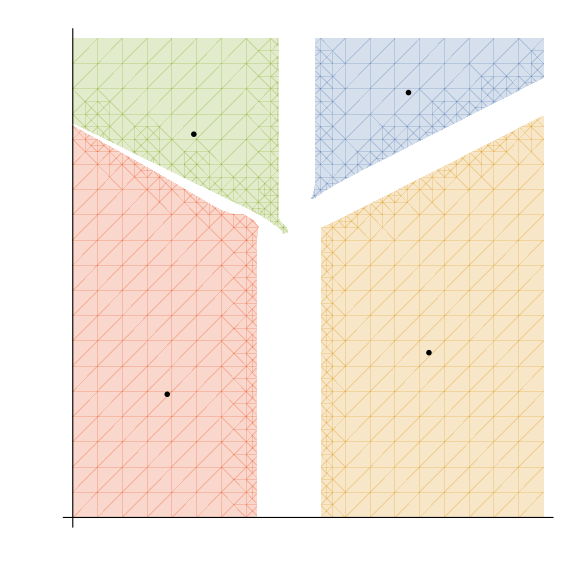

```mathematica
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-4]-(-1)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-4]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]},"NumericalFunction"->False];
rplotb=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-4]-(-3)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-4]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]},"NumericalFunction"->False];
rplotc=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-4]-(0)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-4]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[3]]},"NumericalFunction"->False];
rplotd=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-4]-(2)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-4]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[4]]},"NumericalFunction"->False];
exp1=text[-1.0,-10.5,MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-2,2,MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-12.5,0,MaTeX["\sim q^{0} \omega^{0}",Magnification->3.5],GrayLevel[0],fs];
exp4=text[-13.8,-12.5,MaTeX["\sim q^{4} \omega^{2}",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
Show[rplota,rplotb,rplotc,rplotd,exp1,exp2,exp3,exp4,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=10^{-4}; \; \sigma=10^{-3}",Magnification->3.5]]
```

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((0.105187 ⅇ^(-500000 (-1/1000+dps)^2) √(-dps^2+0.0000112884 Abs[Log[Abs[dps]]]))/((0.0000111627-0.0162378 dps)^2-0.000263665 dps^2+2.97634×10^-9 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-1928.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2054.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1928.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((4.50343×10^-29 ⅇ^(-500000 (-1/1000+dps)^2) √(-dps^2+1.×10^-6 Abs[Log[Abs[dps]]]))/((8.74336×10^-7-3.35983×10^-16 dps)^2-1.12884×10^-31 dps^2+1.12884×10^-37 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-1928.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2054.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14232.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((0.000825465 ⅇ^(-500000 (-1/1000+dps)^2) √(-dps^2+6.15849×10^-11 Abs[Log[Abs[dps]]]))/((-1.25602×10^-7-0.00143845 dps)^2-2.06913×10^-6 dps^2+1.27427×10^-16 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857092504812431879471163024351163426582104629861190599283}. NIntegrate obtained 552.19559102919839959104554592808670116478425325284892619468305755874-0.0035902489938459128206960866382310231314112180489670467812394094963527 ⅈ and 0.0055290640989853211706093036032709599662547777572835869310385565186463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.000025521015728491960361283207476159189323929453322527358204886183469312}. NIntegrate obtained -3.9771059562123709768563331759043844105516196456977964039521151213915 and 9.3956108796455264661866241499398580753543036131069172419262863925342×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00025482984479425963486303027010513903841387683140406798600622657231396}. NIntegrate obtained -3.580384542204669191552151133930302512519023008989472708184004502063-5.9816255991681966332840924102447075855460198108282710828663262570722×10^-6 ⅈ and 6.6115024890504076698897405340672789414909292823021151849685435952461×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/1000+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/1000+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/1000+dps)^2) √(2/π) ((4.00002×10^-32 √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])-(1.×10^-32 (-4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps) dps-4.00002×10^-32 dps^2+4.00003×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857078649866975616039967490286052126863416717624271455948}. NIntegrate obtained 5.2940075578849407412554698966229617295913398473253228273630141439363-9.7306512811997310042141170459580108522829073560644448497700574824302×10^-8 ⅈ and 9.2963403946717594649750106653456912319051482409725025105555487804028×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857092504812431879471163024351163426582104629861190599283}. NIntegrate obtained 552.19559102919839959104554592808670116478425325284892619468305755874-0.0035902489938459128206960866382310231314112180489670467812394094963527 ⅈ and 0.0055290640989853211706093036032709599662547777572835869310385565186463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-2.496939045509039596957179400680804616505198340244318868568220926366×10^-6}. NIntegrate obtained 78.505319349090561408385529519391725685044327489715938483906518935026-8.6800289426448403299976924283325215185131584603925544537814887168528×10^-7 ⅈ and 1.2997015772939490254456892047787044155518020951604950007564423823312×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

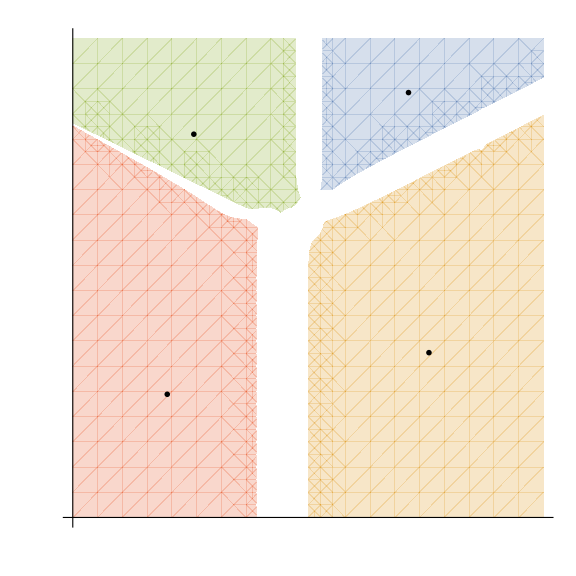

```mathematica
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-3]-(-1)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]},"NumericalFunction"->False];
rplotb=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-3]-(-3)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]},"NumericalFunction"->False];
rplotc=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-3]-(0)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[3]]},"NumericalFunction"->False];
rplotd=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-3]-(2)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[4]]},"NumericalFunction"->False];
exp1=text[-1.0,-10.5,MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-2,2,MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-12.5,0,MaTeX["\sim q^{0} \omega^{0}",Magnification->3.5],GrayLevel[0],fs];
exp4=text[-13.8,-12.5,MaTeX["\sim q^{4} \omega^{2}",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
Show[rplota,rplotb,rplotc,rplotd,exp1,exp2,exp3,exp4,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=10^{-3}; \; \sigma=10^{-3}",Magnification->3.5]]
```

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/100+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/100+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((0.105187 ⅇ^(-500000 (-1/100+dps)^2) √(-dps^2+0.000127427 Abs[Log[Abs[dps]]]))/((0.000127302-0.0162378 dps)^2-0.000263665 dps^2+3.35981×10^-8 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-1410.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2671.07] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1410.03] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.013245049125726238135614412989149457975736304154553817500192583794325}. NIntegrate obtained 0.013259902989746775973063572163580104536038264375547073504866329706458 and 6.8519517366366447068634650033354311062373172839497491261700009482799×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.013086053658238710765442259016879486961432657665529821030766721741396}. NIntegrate obtained 0.15958643194580004632313108874189415051707334408118825462306921847597 and 8.969045173699320105881151911223020908747235699272517317447671981265×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.013086053658238710765442259016879486961432657665529821030766721741396}. NIntegrate obtained -0.16793121982839344615644447633872194279523268640183876351218396152826 and 9.4606164215238900926434868419600800914942487191395651341377660184973×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/100+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/100+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((4.50343×10^-29 ⅇ^(-500000 (-1/100+dps)^2) √(-dps^2+0.000127427 Abs[Log[Abs[dps]]]))/((0.000127302-3.35983×10^-16 dps)^2-1.12884×10^-31 dps^2+1.43846×10^-35 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

General::munfl: Exp[-1410.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2671.07] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1410.03] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.013245049125726238135614412989149457975736304154553817500192583794325}. NIntegrate obtained 0.0044472856489822754877021868018633515990751367319821691933763936698558 and 1.8656109212863778797849560293836162435712190063887381294763924855192×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.013086053658238710765442259016879486961432657665529821030766721741396}. NIntegrate obtained 0.0041399285048161741116203739283925565046926841840963062332144949207441 and 2.2036994173723545118749507419054123670331295137699361035736553238049×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/100+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/100+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function ((0.105187 ⅇ^(-500000 (-1/100+dps)^2) √(-dps^2+4.83294×10^-13 Abs[Log[Abs[dps]]]))/((-1.25663×10^-7-0.0162378 dps)^2-0.000263665 dps^2+1.27427×10^-16 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-2.496939045509039596957179400680804616505198340244318868568220926366×10^-6}. NIntegrate obtained 2.4789994900625830839723925337909634421311117596088392374808831914342×10^-20-2.7080112699791564897834538921093808820096457843279607256516844977664×10^-28 ⅈ and 4.0854938977448181883965428006185141285774776954492134527746051049634×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-8.0016374576724895319274160918981999016931041218693590103227969040211×10^-6}. NIntegrate obtained -2.6650497091667731268639775563296566789858386170170118503074168682288×10^-21 and 2.5569816892950750198042091890746134705530165897736600883160170047672×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-2.496939045509039596957179400680804616505198340244318868568220926366×10^-6}. NIntegrate obtained -9.0284987700918729353705462707853649344952431800648816079769441331224×10^-22-2.3088370902857960056641399517874972444189495817964785205098359842×10^-27 ⅈ and 3.6161319692602306406644186656067678332771930799648244315796265517619×10^-27 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((3.98944×10^-30 ⅇ^(-500000 (-1/100+dps)^2) √(-dps^2+1.×10^-16 Abs[Log[Abs[dps]]]))/((-1.25664×10^-7-1.×10^-16 dps)^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/100+dps)^2) √(2/π) (-(1.×10^-32 (4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps)+2.00001×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2)+(1.00001×10^-48 Abs[Log[Abs[dps]]])/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]])))) is less than WorkingPrecision (18.).

NIntegrate::precw: The precision of the argument function (500 ⅇ^(-500000 (-1/100+dps)^2) √(2/π) ((4.00002×10^-32 √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])-(1.×10^-32 (-4.00001×10^-16 (-1.25664×10^-7-1.×10^-16 dps) dps-4.00002×10^-32 dps^2+4.00003×10^-48 Abs[Log[Abs[«1»]]]) √(-dps^2+1.×10^-16 Abs[Log[«1»]]))/(((-1.25664×10^-7+Times[«2»])^2-1.×10^-32 dps^2+1.00001×10^-48 Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.000080932318402857078649866975616039967490286052126863416717624271455948}. NIntegrate obtained 1.3722947542272625673796267513072042710697436563773595831087124917881×10^-44-2.4275965581688702163596555425164927499692251174402496118962632188992×10^-52 ⅈ and 3.3073207712384253643053214453636371796484312655579722286527724692711×10^-52 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.000080932318402857078649866975616039967490286052126863416717624271455948}. NIntegrate obtained 1.7486799860246595544424543226716144941630361079635453525687987632074×10^-42-3.0934239909640505363385427272611981471387227022205881541872585155608×10^-50 ⅈ and 4.2144339779863669617993514058163054682843212514347932017041604951675×10^-50 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {0.000080932318402857078649866975616039967490286052126863416717624271455948}. NIntegrate obtained 2.2282980271201186084738093980789117470895358841078796882783037797645×10^-40-3.9418708002544918642014457193796774126890066947892715455770351482754×10^-48 ⅈ and 5.3703450566250928282035978580767488576838373298901486070793198157177×10^-48 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

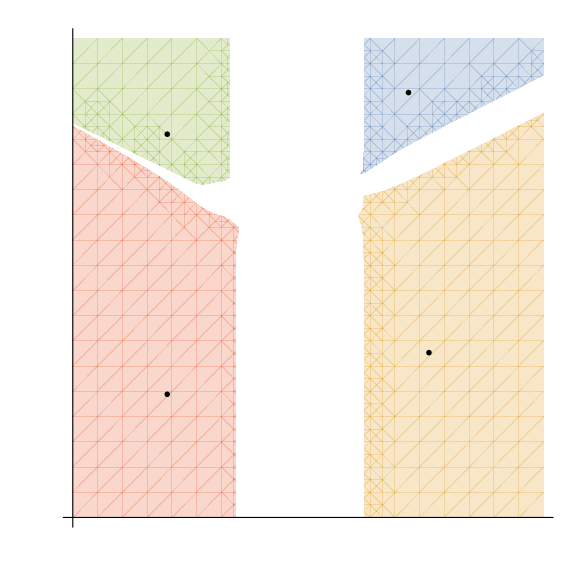

```mathematica
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-2]-(-1)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-2]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]},"NumericalFunction"->False];
rplotb=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-2]-(-3)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-2]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]},"NumericalFunction"->False];
rplotc=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-2]-(0)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-2]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[3]]},"NumericalFunction"->False];
rplotd=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-3,10^-2]-(2)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-3,10^-2]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[4]]},"NumericalFunction"->False];
exp1=text[-1.0,-10.5,MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-2,2,MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-13.8,0,MaTeX["\sim q^{0} \omega^{0}",Magnification->3.5],GrayLevel[0],fs];
exp4=text[-13.8,-12.5,MaTeX["\sim q^{4} \omega^{2}",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
Show[rplota,rplotb,rplotc,rplotd,exp1,exp2,exp3,exp4,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=10^{-2}; \; \sigma=10^{-3}",Magnification->3.5]]
```